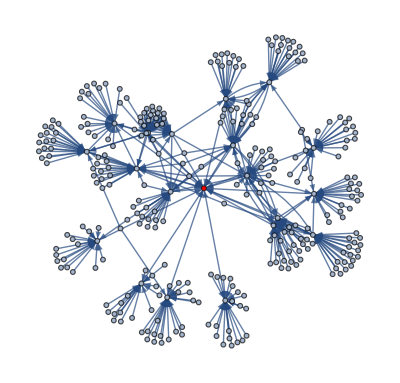

```mathematica
links=WikipediaData["PageRank","BacklinksRules","MaxLevelItems"->20,"MaxLevel"->2];
g=Graph[links,VertexLabels->Placed["Name",Tooltip],VertexStyle->{"PageRank"->Red}]
```

```mathematica
Column[Part[VertexList[g],Ordering[PageRankCentrality[g,0.99],All,Greater]]]
```

PageRank
List of algorithms
Spamdexing
Carl Linnaeus
Google Search
Ray Kurzweil
Web crawler
Semantic network
History of the Internet
Telecommunications network
Network topology
Wide area information server
Web indexing
Web server
Semantic Web
Knowbot
HTTPS
HTML
Search engine spammer
Search engine optimization
Telemarketing
DNSBL
Spamdex
Keyword spamming
Spamming
Search engine (computing)
Meta element
Semantics
Mind map
Knowledge representation and reasoning
Joke
Hypertext Transfer Protocol
Graph theory
Dublin Core
List of artificial intelligence projects
February 12
Douglas Hofstadter
Dan Bricklin
Donald Knuth
Craig Venter
Chinese room
Bertrand Russell
Bill Joy
Bjarne Stroustrup
Artificial intelligence
Telecommunications in Brazil
Dijkstra's algorithm
Search algorithm
Heap (data structure)
Error detection and correction
Earley parser
Context-free grammar
Algorithm
Telecommunications in Botswana
Telecommunications in Belgium
Telecommunications in Belarus
Analog television
Analytical Engine
Telecommunications in Anguilla
Amplitude modulation
Telecommunications in Antigua and Barbuda
Analog signal
Alexander Graham Bell
Klingon language
Jennifer Lopez
Iran
Internet
Greg Egan
FAQ
AOL
Anna Kournikova
Amaryllis
Aloe
Agapanthus africanus
Amaranth
Alfred Russel Wallace
Acacia sensu lato
Abalone
Apiaceae
Asteraceae
Aristotle

```mathematica
Column[Sort[PageRankCentrality[g,0.99]]//Reverse]
```

0.258464
0.0535957
0.0462432
0.0425182
0.0396881
0.0382788
0.0382788
0.0346333
0.024018
0.020311
0.0194386
0.0178397
0.0178397
0.0177073
0.0174151
0.0172075
0.0140187
0.0135942
0.00701365
0.00701365
0.00701365
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677
0.000857677

```mathematica
Column[Part[VertexList[g],Ordering[PageRankCentrality[g,0.85],All,Greater]]]
```

PageRank
Web crawler
Spamdexing
Search engine optimization
Google Answers
List of algorithms
Sergey Brin
Larry Page
Percolation theory
Google Search
Ray Kurzweil
South East England
Carl Linnaeus
Markov chain
Hyperlink
Semantic network
Advogato
Bradford's law
Telecommunications network
Network topology
History of the Internet
Internet Archive
Bot
Web spider
Robots exclusion standard
WebCrawler
Web server
Knowbot
HTTPS
Bletchley Park
Mobile phone spam
Newsgroup spam
Messaging spam
Referrer log spam
Server-side redirect
MediaWiki
Anti-spam techniques
Search Engine Spamming
Link farm
Search engine spammer
Telemarketing
DNSBL
Spamdex
Keyword spamming
Spamming
Economy of the United Kingdom
Geography of the United Kingdom
Suburb
Shepherd Neame Brewery
Renewable energy
Pub
Portsmouth
Oxford
London
Kent
Isle of Wight
Hampshire
Hastings
List of Roman place names in Britain
Emsworth
England
Cotswolds
Cornwall
Australian English
Alfred the Great
National Science Foundation
Moffett Federal Airfield
Los Altos Hills, California
List of Russian people
Hamburger
Prince George's County, Maryland
Los Altos, California
Generation X
August 21
Aggression
EuroWordNet
Resource Description Framework
Ontology (information science)
WordNet
Universal Networking Language
Uniform Resource Identifier
Semantic Web
Semantics
Mind map
Knowledge representation and reasoning
Joke
Dublin Core
List of artificial intelligence projects
Seo
Editing
Web directory
Unintended consequences
The Weather Channel
Content management system
List of computing and IT abbreviations
Wide area information server
Domain name
Web banner
Web design
Web indexing
Blog
Search engine (computing)
Optimization (disambiguation)
Meta element
Transhumanism
Technology
Steve Wozniak
Resurrection
Robert Freitas
Philip Glass
Kevin Warwick
K. Eric Drexler
Hugo de Garis
February 12
Douglas Hofstadter
Dan Bricklin
Donald Knuth
Craig Venter
Chinese room
Bertrand Russell
Bill Joy
Bjarne Stroustrup
Artificial intelligence
Koch snowflake
L-system
Complex system
Sierpinski triangle
Sierpinski carpet
Self-similarity
Statistical mechanics
Recursion
Mandelbrot set
Fermi paradox
Fractal
Equation of state
Entropy
Cantor set
Brownian motion
Benoit Mandelbrot
Computing
Stochastic process
Colorless green ideas sleep furiously
White noise
Burst error
Genetic algorithm
The Illuminatus! Trilogy
Travelling salesman problem
Speech recognition
Rock–paper–scissors
Russia
Pseudorandomness
Artificial neural network
Numerical analysis
Laplace transform
Entropy (information theory)
Gibberish
Game theory
Finite-state machine
Chain reaction
Andrey Markov
Borůvka's algorithm
Alpha–beta pruning
Best-first search
A* search algorithm
Depth-first search
Breadth-first search
Prim's algorithm
Kruskal's algorithm
Dijkstra's algorithm
Search algorithm
Heap (data structure)
Error detection and correction
Earley parser
Context-free grammar
Algorithm
Okemos, Michigan
Natural language understanding
Richard Branson
Trillian (software)
List of inventors
Agrigento
1973
1998
University of Michigan
September 4
Stanford University
March 26
Motorola
Lansing, Michigan
List of programmers
List of computer scientists
Mass media
LaTeX
Internet Relay Chat
History of Wikipedia
HyperCard
Hypertext
Hypertext Transfer Protocol
HTML
Graph theory
Graphical user interface
File viewer
Expert
Document Object Model
Database
Context menu
Telecommunications in Canada
BT Group
Bluetooth
Beacon
Bell Labs
Communications in Burundi
Telecommunications in Burkina Faso
Telecommunications in Brunei
Telecommunications in the British Virgin Islands
Telecommunications in Brazil
Telecommunications in Botswana
Telecommunications in Belgium
Telecommunications in Belarus
Analog television
Analytical Engine
Telecommunications in Anguilla
Amplitude modulation
Telecommunications in Antigua and Barbuda
Analog signal
Alexander Graham Bell
Case sensitivity
Klondike (solitaire)
2000s (decade)
Website
Web browser
World Wide Web
Wiki
René Descartes
Lycos
Klingon language
Jennifer Lopez
Iran
Internet
Greg Egan
FAQ
AOL
Anna Kournikova
Googleplex
DoubleClick
AdSense
Google Toolbar
Gmail
Google Groups
Google News
Orkut
List of search engines
Google Shopping
Google (verb)
Blogger (service)
Googlebot
Google bomb
Shirley M. Tilghman
Eric Schmidt
Brassicaceae
Bird
Baruch Spinoza
Ansbach
Artemis
Anders Celsius
Ant
Aurochs
Arctic fox
Antoine Lavoisier
Amaryllis
Aloe
Agapanthus africanus
Amaranth
Alfred Russel Wallace
Acacia sensu lato
Abalone
Apiaceae
Asteraceae
Aristotle
Subject (documents)
Samuel C. Bradford
Bradford law
Preferential attachment
Outline of library science
Bibliogram
List of eponymous laws
List of terms relating to algorithms and data structures
Scientific phenomena named after people
List of scientific laws named after people
Relevance (information retrieval)
1934 in science
Bradford (disambiguation)
Pareto distribution
Zipf's law
Advogato.org
System prevalence
Sybil attack
Abaco (web browser)
Reputation system
Linux Game Publishing
List of social networking websites
Raph Levien
Open and Free Technology Community
List of Quakers
Trust metric
Gna!
AdvoWiki
TeX
Interwiki links
Guild

```mathematica
Column[Sort[PageRankCentrality[g,0.85]]//Reverse]
```

0.217547
0.0446832
0.0388179
0.0359888
0.0355662
0.0338277
0.0333257
0.0333257
0.0247054
0.021234
0.0206476
0.0194467
0.0194467
0.0189875
0.0185422
0.0182969
0.0153143
0.0148551
0.00773816
0.00773816
0.00773816
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037
0.00108037

```mathematica
Column[Part[VertexList[g],Ordering[PageRankCentrality[g,0.1],All,Greater]]]
```

PageRank
South East England
Carl Linnaeus
Markov chain
Ray Kurzweil
Percolation theory
List of algorithms
Spamdexing
Google Answers
Google Search
Semantic network
Advogato
Search engine optimization
Hyperlink
Bradford's law
Web crawler
Sergey Brin
Larry Page
Telecommunications network
Network topology
History of the Internet
Internet Archive
Bot
Web spider
Robots exclusion standard
WebCrawler
Web server
Knowbot
HTTPS
Bletchley Park
Mobile phone spam
Newsgroup spam
Messaging spam
Referrer log spam
Server-side redirect
MediaWiki
Anti-spam techniques
Search Engine Spamming
Link farm
Search engine spammer
Telemarketing
DNSBL
Spamdex
Keyword spamming
Spamming
Economy of the United Kingdom
Geography of the United Kingdom
Suburb
Shepherd Neame Brewery
Renewable energy
Pub
Portsmouth
Oxford
London
Kent
Isle of Wight
Hampshire
Hastings
List of Roman place names in Britain
Emsworth
England
Cotswolds
Cornwall
Australian English
Alfred the Great
National Science Foundation
Moffett Federal Airfield
Los Altos Hills, California
List of Russian people
Hamburger
Prince George's County, Maryland
Los Altos, California
Generation X
August 21
Aggression
EuroWordNet
Resource Description Framework
Ontology (information science)
WordNet
Universal Networking Language
Uniform Resource Identifier
Semantic Web
Semantics
Mind map
Knowledge representation and reasoning
Joke
Dublin Core
List of artificial intelligence projects
Seo
Editing
Web directory
Unintended consequences
The Weather Channel
Content management system
List of computing and IT abbreviations
Wide area information server
Domain name
Web banner
Web design
Web indexing
Blog
Search engine (computing)
Optimization (disambiguation)
Meta element
Transhumanism
Technology
Steve Wozniak
Resurrection
Robert Freitas
Philip Glass
Kevin Warwick
K. Eric Drexler
Hugo de Garis
February 12
Douglas Hofstadter
Dan Bricklin
Donald Knuth
Craig Venter
Chinese room
Bertrand Russell
Bill Joy
Bjarne Stroustrup
Artificial intelligence
Koch snowflake
L-system
Complex system
Sierpinski triangle
Sierpinski carpet
Self-similarity
Statistical mechanics
Recursion
Mandelbrot set
Fermi paradox
Fractal
Equation of state
Entropy
Cantor set
Brownian motion
Benoit Mandelbrot
Computing
Stochastic process
Colorless green ideas sleep furiously
White noise
Burst error
Genetic algorithm
The Illuminatus! Trilogy
Travelling salesman problem
Speech recognition
Rock–paper–scissors
Russia
Pseudorandomness
Artificial neural network
Numerical analysis
Laplace transform
Entropy (information theory)
Gibberish
Game theory
Finite-state machine
Chain reaction
Andrey Markov
Borůvka's algorithm
Alpha–beta pruning
Best-first search
A* search algorithm
Depth-first search
Breadth-first search
Prim's algorithm
Kruskal's algorithm
Dijkstra's algorithm
Search algorithm
Heap (data structure)
Error detection and correction
Earley parser
Context-free grammar
Algorithm
Okemos, Michigan
Natural language understanding
Richard Branson
Trillian (software)
List of inventors
Agrigento
1973
1998
University of Michigan
September 4
Stanford University
March 26
Motorola
Lansing, Michigan
List of programmers
List of computer scientists
Mass media
LaTeX
Internet Relay Chat
History of Wikipedia
HyperCard
Hypertext
Hypertext Transfer Protocol
HTML
Graph theory
Graphical user interface
File viewer
Expert
Document Object Model
Database
Context menu
Telecommunications in Canada
BT Group
Bluetooth
Beacon
Bell Labs
Communications in Burundi
Telecommunications in Burkina Faso
Telecommunications in Brunei
Telecommunications in the British Virgin Islands
Telecommunications in Brazil
Telecommunications in Botswana
Telecommunications in Belgium
Telecommunications in Belarus
Analog television
Analytical Engine
Telecommunications in Anguilla
Amplitude modulation
Telecommunications in Antigua and Barbuda
Analog signal
Alexander Graham Bell
Case sensitivity
Klondike (solitaire)
2000s (decade)
Website
Web browser
World Wide Web
Wiki
René Descartes
Lycos
Klingon language
Jennifer Lopez
Iran
Internet
Greg Egan
FAQ
AOL
Anna Kournikova
Googleplex
DoubleClick
AdSense
Google Toolbar
Gmail
Google Groups
Google News
Orkut
List of search engines
Google Shopping
Google (verb)
Blogger (service)
Googlebot
Google bomb
Shirley M. Tilghman
Eric Schmidt
Brassicaceae
Bird
Baruch Spinoza
Ansbach
Artemis
Anders Celsius
Ant
Aurochs
Arctic fox
Antoine Lavoisier
Amaryllis
Aloe
Agapanthus africanus
Amaranth
Alfred Russel Wallace
Acacia sensu lato
Abalone
Apiaceae
Asteraceae
Aristotle
Subject (documents)
Samuel C. Bradford
Bradford law
Preferential attachment
Outline of library science
Bibliogram
List of eponymous laws
List of terms relating to algorithms and data structures
Scientific phenomena named after people
List of scientific laws named after people
Relevance (information retrieval)
1934 in science
Bradford (disambiguation)
Pareto distribution
Zipf's law
Advogato.org
System prevalence
Sybil attack
Abaco (web browser)
Reputation system
Linux Game Publishing
List of social networking websites
Raph Levien
Open and Free Technology Community
List of Quakers
Trust metric
Gna!
AdvoWiki
TeX
Interwiki links
Guild

```mathematica
Column[Sort[PageRankCentrality[g,0.1]]//Reverse]
```

0.011429
0.00872074
0.00872074
0.00857539
0.00839825
0.00820625
0.00818053
0.00812076
0.00805142
0.0079482
0.00756645
0.00741263
0.00738884
0.00733662
0.00726728
0.00724466
0.0071456
0.0071456
0.00501442
0.00501442
0.00501442
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691
0.00290691

WebSearch::nval: Invalid value for parameter Language in service BingSearch.

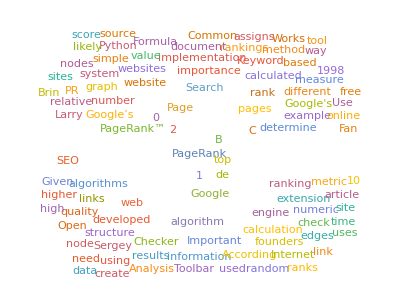

```mathematica
WordCloud[DeleteStopwords[Join@@TextWords/@WebSearch["PageRank","Snippets",MaxItems->200]]]
```